```mathematica
Predicting Silver Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

## Resources

- KAG/USDT hourly price: Recent (≥ 2025) Bitmart data through API.

## In This Notebook

LPPLS model implementation (2026 ed.) for Silver price in USD.
Uses KAG price as a proxy for Silver’s price, due to current lack of access to high quality (hourly) Spot Silver price data.

```mathematica
base=DirectoryName[NotebookFileName[]];
lastPriceDate=DateString[Yesterday,"ISODate"]
```

2026-01-20

```mathematica
hourlyPricesCsv=base<>"KAG_USDT_1h.csv";
prices =Import[hourlyPricesCsv, HeaderLines->1]
```

```mathematica
(* First price date: *)
firstDownloadedDateTime=prices[[1]][[1]];
{firstDownloadedDate,firstDownloadedTime}=StringSplit[firstDownloadedDateTime];
firstPriceDate=firstDownloadedDate
```

2020-10-31

```mathematica
(* Some freshness checks: *)
lastDownloadedDateTime=prices[[2]][[2]];
{lastDownloadedDate, lastDownloadedTime}=StringSplit[lastDownloadedDateTime]
{DateString[DatePlus[lastDownloadedDate, 0], "ISODate"]==lastPriceDate, lastDownloadedTime=="23:00:00"}
```

{2026-01-20,23:00:00}

{True,True}

```mathematica
closingPrices={#[[1]],#[[7]]}&/@prices
```

```mathematica
(* Filter non-numerical values *)
closingPricesFilter=Select[closingPrices, NumberQ[#[[2]]]&]
```

```mathematica
(* Convert to seconds *)
hourlyPricesTs={#[[1]]/1000, #[[2]]}&/@closingPricesFilter
```

```mathematica
(* Hourly data *)
hourlyPrices=SortBy[hourlyPricesTs, First]
```

```mathematica
Length[hourlyPrices]
```

45788

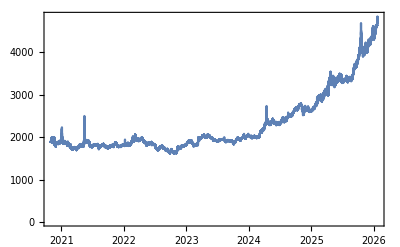

```mathematica
DateListPlot[hourlyPrices,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
Export[base<>"csv/Silver(KAG)_price-hourly-"<>StringDelete[firstPriceDate, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv",hourlyPrices]
```

```mathematica
{FromUnixTime[hourlyPrices[[1]][[1]]],FromUnixTime[hourlyPrices[[-1]][[1]]]}
```

{Sat 31 Oct 2020 05:00:00GMT+1,Wed 21 Jan 2026 00:00:00GMT+1}

```mathematica
(* Use the Log Price *)
logPrice= {#[[1]], Log[#[[2]]]}&/@hourlyPrices
```

```mathematica
(* Appendix 5.1. Example: Analyze / predict the 2026 bubble turning point: *)
(* Generalized to multiple bubbles *)
bubblesDate={{"2024-01-01", lastPriceDate}, {"2025-01-01", lastPriceDate}}
```

{{2024-01-01,2026-01-20},{2025-01-01,2026-01-20}}

```mathematica
bubbleN=Length[bubblesDate]
```

2

```mathematica
(* Timestamp indexes: *)
bubblesTimestampIndex={UnixTime[#[[1]]], UnixTime[#[[2]]]}&/@bubblesDate
```

{{1704063600,1768863600},{1735686000,1768863600}}

```mathematica
bubblesDays=(#[[2]]-#[[1]])/86400&/@bubblesTimestampIndex
```

{750,384}

```mathematica
bubbles=Table[Select[logPrice,bubblesTimestampIndex[[i]][[1]]≤#[[1]]≤ bubblesTimestampIndex[[i]][[2]]&], {i, bubbleN}];
#[[1]]&/@bubbles
```

{{1704063600,7.61955},{1735686000,7.87335}}

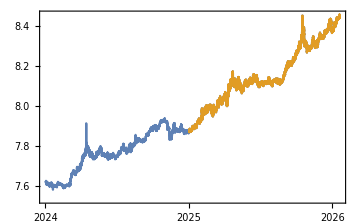

```mathematica
DateListPlot[bubbles, ImageSize->Medium, DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically *)
scaleH[data_]:= Module[{peaks, first},
(* Scale bubbles horizontally (0-1) (set 1 at the true peaks) *)
peaks=MaximalBy[data, Last][[1]];
first = data[[1]];
{(#[[1]]-first[[1]])/(peaks[[1]]-first[[1]]),#[[2]]}&/@data
]
```

```mathematica
scaleV[data_]:= Module[{min, max},
(* Rescale vertically *)
min=Min[Last /@data];
max=Max[Last /@data];
{#[[1]],(#[[2]]-min)/(max-min)}&/@data
]
```

```mathematica
bubblesScaled=scaleV[scaleH[#]]&/@ bubbles//N;
#[[-1]]&/@bubblesScaled
```

{{1.00039,0.990083},{1.00076,0.985239}}

```mathematica
Length/@bubblesScaled
```

{18001,9217}

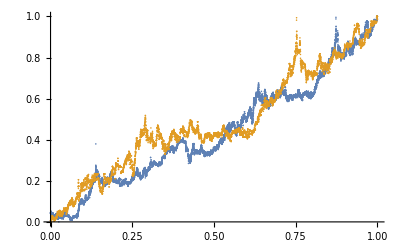

```mathematica
(* LPPLS model over the scaled bubbles: *)
(* Step 1. Identify initial error model: *)
(* 1.a Fit the log market cap with a flexible nonparametric curve. *)
ListPlot[bubblesScaled]
```

```mathematica
(* Export bubbles data: *)
bubbleScaledCsvs=MapIndexed[Export[base<>"csv/bubbleScaled-Silver(KAG)"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,bubblesScaled]
```

```mathematica
(* Our "goodness of fit" control parameter. The smaller the better. i.e. stricter hypothesis testing will be. *)
(* Empirically, spans greater than 0.1 indicate that our prediction is not very reliable / trustworthy. *)bestSpan=0.1
```

0.1

```mathematica
(* Get params from R: *)
rInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@bubbleScaledCsvs;
```

```mathematica
rRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@rInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
rParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@rRuns
```

{{15.6952,17980.3},{15.7242,9196.28}}

```mathematica
(* {RSS, SE, SE of the fit}: *)
rErrors=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-6;;;;2]]&/@rRuns
```

{{7.04368,0.019793,0.00105602},{5.96404,0.0254675,0.00188422}}

```mathematica
(* Use Loess: *)
LoessR=ResourceFunction["Loess"]
```

```mathematica
bestFits = LoessR[#, Scaled[bestSpan], #[[All, 1]], {InterpolationOrder-> 1}]&/@bubblesScaled;
```

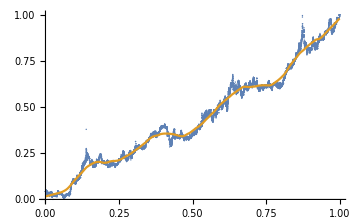
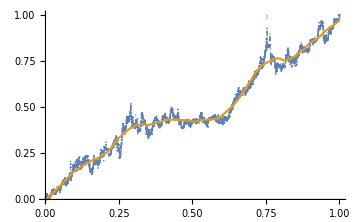

```mathematica
Show[ListPlot[#, ImageSize->Medium],   ListLinePlot[{{{0,0}},Table[{t, LoessR[#, Scaled[bestSpan], t ]}, {t, Min[#[[All, 1]]], Max[#[[All, 1]]], .005}]}]]&/@bubblesScaled
```

```mathematica
(* 1.b Detrend: *)
ℛs = Table[bubblesScaled[[i]][[All,2]]-bestFits[[i]], {i, bubbleN}];
```

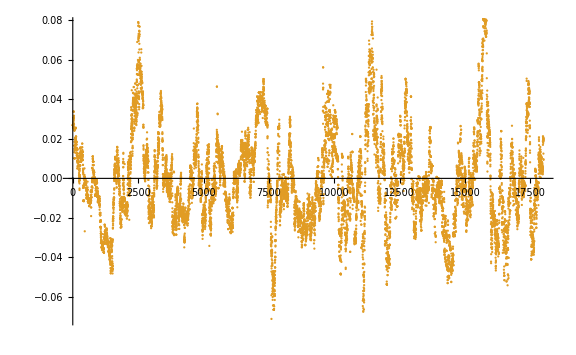
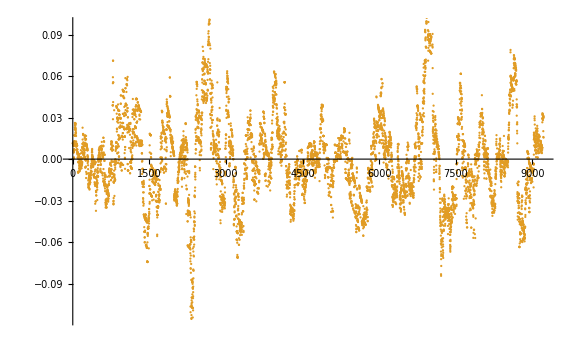

```mathematica
(* Plot residuals: *)
ListPlot[{{0,0},#}, ImageSize->Large]&/@ℛs
```

```mathematica
(* Standard deviations: *)
stdDevℛs=StandardDeviation /@ℛs
```

{0.023851,0.0307914}

```mathematica
(* Standardized residuals: *)
stdℛs = MapThread[#1/#2&,{ℛs, stdDevℛs}];
```

```mathematica
(* RSS: *)
ℛsSS =Total[#^2]&/@ℛs
```

{10.2445,8.73805}

```mathematica
(* Larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[1]]]&,{ℛsSS,rErrors}]
```

{10.2445 > 7.04368,8.73805 > 5.96404}

```mathematica
(* Residual Standard Error(s): *)
ℛsSEs=MapThread[√(Total[#1^2]/(Length[#1]-#2[[1]]))&,{ℛs,rParams}]
```

{0.0238663,0.0308165}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0238663 > 0.019793,0.0308165 > 0.0254675}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(Length[#1]-#2[[1]]))&,{ℛs,rParams, rErrors}]
```

{0.0197898,0.0254593}

```mathematica
ℛsSEs=MapThread[√(Total[#1^2]/(#2[[2]]))&,{ℛs,rParams}]
```

{0.0238696,0.0308249}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0238696 > 0.019793,0.0308249 > 0.0254675}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(#2[[2]]))&,{ℛs,rParams, rErrors}]
```

{0.0197925,0.0254662}

```mathematica
(* 3. Fit LPPLS function: *)
tc=.
numParams=7;
lpplsModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Select first bubble for fitting: *)
bubble=1
```

```mathematica
(* Or, select last bubble for fitting: *)
bubble=bubbleN
```

2

```mathematica
(* Use the selected bubble: *)
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
(* Use the params for the selected bubble: *)
{estimatedNParams, effectiveDfs}=rParams[[bubble]]
```

{15.7242,9196.28}

```mathematica
(* Profiling over 0.1 < m < 1, 3 < ω < 14 and 1. < tc < 3 months in the future *)
minM=0.1;
maxM=1;
minω=3;
maxω=14;
months=3;
```

```mathematica
(* Try to estimate all the params using log-likelihood: *)
(* Define `months` in the future scaled interval endpoint: *)
bubbleScaled[[-1]][[1]]
maxTc=bubbleScaled[[-1]][[1]]+(bubblesDays[[bubble]]+30 months)/bubblesDays[[bubble]]//N
```

1.00076

2.23514

```mathematica
(* Define 7 days resolution scaled interval step: *)
stepTc=7/bubblesDays[[bubble]]//N
```

0.0182292

```mathematica
(* Define 10 days resolution scaled initial time step *)
stepTi=10/bubblesDays[[bubble]]//N
```

0.0260417

```mathematica
(* Slow. Shortcut below *)
Now[]
fits=
Table[m=.;tc=.;
bestFit=MaximalBy[Flatten[ParallelTable[{tc,m,ω,nlm=NonlinearModelFit[Select[bubbleScaled,#[[1]]>= t1&],lpplsModel,{a,b,c,d}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
RSS=Total[ℛ^2],
RSS/(Length[ℛ]-numParams),
StandardDeviation[ℛ],
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10}, {ω,minω,maxω,1./10},  {tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],2], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[4]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]], ω-> bestFit[[3]], RSS-> bestFit[[6]],ℛerror-> bestFit[[7]], ℛσ-> bestFit[[8]],LL-> bestFit[[9]]},bestFit[[5]]], {t1, Range[0,1/2+stepTi, stepTi]}]//AbsoluteTiming
```

Wed 21 Jan 2026 14:39:28GMT+1[]

{24173.3,{{a→1.06555,b→-0.977289,c→-0.0694949,d→-0.103473,T_1→0.,tc→1.01909,m→0.7,ω→6.2,RSS→11.1601,ℛerror→0.00121174,ℛσ→0.0347987,LL→30144.,ρ→0.96447,σ→-0.00919304,μ→-2.22062×10^-17},{a→1.09173,b→-0.991597,c→-0.0607438,d→-0.105943,T_1→0.0260417,tc→1.03732,m→0.7,ω→6.5,RSS→11.0912,ℛerror→0.00123648,ℛσ→0.0351518,LL→29253.9,ρ→0.964346,σ→-0.0093022,μ→-2.80583×10^-17},{a→1.09251,b→-0.993454,c→-0.0617438,d→-0.106824,T_1→0.0520833,tc→1.03732,m→0.7,ω→6.5,RSS→11.0478,ℛerror→0.0012655,ℛσ→0.0355616,LL→28404.5,ρ→0.964636,σ→-0.00937302,μ→3.49705×10^-18},{a→1.09372,b→-0.996376,c→-0.0635215,d→-0.107922,T_1→0.078125,tc→1.03732,m→0.7,ω→6.5,RSS→10.9658,ℛerror→0.00129162,ℛσ→0.0359264,LL→27556.4,ρ→0.964778,σ→-0.00945038,μ→-1.95451×10^-18},{a→1.02475,b→-0.976563,c→-0.0751039,d→-0.130773,T_1→0.104167,tc→1.01909,m→0.8,ω→6.1,RSS→10.4019,ℛerror→0.00126083,ℛσ→0.0354953,LL→26867.4,ρ→0.964558,σ→-0.00936567,μ→-1.57358×10^-17},{a→1.0282,b→-0.987341,c→-0.0938341,d→-0.127792,T_1→0.130208,tc→1.01909,m→0.8,ω→6.2,RSS→9.3075,ℛerror→0.00116198,ℛσ→0.0340751,LL→26183.3,ρ→0.962288,σ→-0.00926898,μ→2.00079×10^-17},{a→0.995406,b→-0.997119,c→-0.111812,d→-0.14906,T_1→0.15625,tc→1.01909,m→0.9,ω→6.2,RSS→8.4411,ℛerror→0.00108623,ℛσ→0.0329453,LL→25440.,ρ→0.960294,σ→-0.0091908,μ→-3.3093×10^-18},{a→0.995563,b→-0.997659,c→-0.112282,d→-0.148997,T_1→0.182292,tc→1.01909,m→0.9,ω→6.2,RSS→8.34769,ℛerror→0.00110844,ℛσ→0.03328,LL→24692.1,ρ→0.961473,σ→-0.00914801,μ→4.05023×10^-17},{a→0.996046,b→-1.00023,c→-0.124992,d→-0.140447,T_1→0.208333,tc→1.01909,m→0.9,ω→6.3,RSS→8.21787,ℛerror→0.00112713,ℛσ→0.0335589,LL→23998.5,ρ→0.963101,σ→-0.00903137,μ→3.99479×10^-17},{a→0.995536,b→-0.997477,c→-0.112401,d→-0.149529,T_1→0.234375,tc→1.01909,m→0.9,ω→6.2,RSS→8.12882,ℛerror→0.00115286,ℛσ→0.0339394,LL→23105.2,ρ→0.962846,σ→-0.00916473,μ→-2.31518×10^-17},{a→1.02356,b→-0.970367,c→-0.0754967,d→-0.147018,T_1→0.260417,tc→1.01909,m→0.8,ω→6.1,RSS→7.26879,ℛerror→0.00106721,ℛσ→0.0326538,LL→22488.6,ρ→0.961726,σ→-0.00894696,μ→5.13681×10^-18},{a→1.02691,b→-0.982581,c→-0.0912108,d→-0.133655,T_1→0.286458,tc→1.01909,m→0.8,ω→6.2,RSS→6.96499,ℛerror→0.0010598,ℛσ→0.0325397,LL→21815.5,ρ→0.96266,σ→-0.00880828,μ→2.54029×10^-17},{a→1.02442,b→-1.03712,c→-0.154534,d→-0.0781969,T_1→0.3125,tc→1.03732,m→0.9,ω→7.,RSS→5.85431,ℛerror→0.000924559,ℛσ→0.0303922,LL→21225.8,ρ→0.959901,σ→-0.00851946,μ→-3.08606×10^-17},{a→1.02047,b→-1.08007,c→-0.183431,d→-0.0236108,T_1→0.338542,tc→1.05555,m→1.,ω→7.7,RSS→5.20526,ℛerror→0.000854442,ℛσ→0.0292165,LL→20496.5,ρ→0.957576,σ→-0.00841896,μ→1.90757×10^-17},{a→1.019,b→-1.07415,c→-0.185817,d→-0.0278614,T_1→0.364583,tc→1.05555,m→1.,ω→7.7,RSS→4.99787,ℛerror→0.000854044,ℛσ→0.0292091,LL→19669.7,ρ→0.957446,σ→-0.00842935,μ→-5.15807×10^-17},{a→1.01934,b→-1.07551,c→-0.185315,d→-0.026818,T_1→0.390625,tc→1.05555,m→1.,ω→7.7,RSS→4.92774,ℛerror→0.000878072,ℛσ→0.0296164,LL→18844.1,ρ→0.958318,σ→-0.00846074,μ→1.68616×10^-17},{a→1.02122,b→-1.02396,c→-0.163449,d→-0.0857253,T_1→0.416667,tc→1.03732,m→0.9,ω→7.,RSS→4.86525,ℛerror→0.000905668,ℛσ→0.0300775,LL→18055.2,ρ→0.959834,σ→-0.00843804,μ→1.48479×10^-17},{a→1.02105,b→-1.08314,c→-0.179202,d→-0.0256594,T_1→0.442708,tc→1.05555,m→1.,ω→7.7,RSS→4.71622,ℛerror→0.000918804,ℛσ→0.0302941,LL→17201.1,ρ→0.959632,σ→-0.00851968,μ→-1.62103×10^-17},{a→1.01945,b→-1.07567,c→-0.185034,d→-0.0243402,T_1→0.46875,tc→1.05555,m→1.,ω→7.7,RSS→4.52248,ℛerror→0.000924276,ℛσ→0.0303833,LL→16352.5,ρ→0.958814,σ→-0.00862902,μ→7.79108×10^-18},{a→1.01668,b→-1.06254,c→-0.198159,d→-0.000894638,T_1→0.494792,tc→1.05555,m→1.,ω→7.8,RSS→4.31996,ℛerror→0.000928424,ℛσ→0.0304504,LL→15481.3,ρ→0.957903,σ→-0.00874112,μ→-2.30004×10^-17},{a→1.01479,b→-1.0531,c→-0.203685,d→0.0255699,T_1→0.520833,tc→1.05555,m→1.,ω→7.9,RSS→4.22231,ℛerror→0.00095679,ℛσ→0.030911,LL→14611.6,ρ→0.957857,σ→-0.00887805,μ→-2.04058×10^-17}}}

```mathematica
(* Shortcut: *)
fits=;
```

```mathematica
(* Timing in hours: *)
fits[[1]]/60/60
```

6.71479

```mathematica
fits=fits[[2]];
```

```mathematica
fits[[All,{5,6,11,12}]]//TableForm
```

T_1→0. | tc→1.01909 | ℛσ→0.0347987 | LL→30144.
T_1→0.0260417 | tc→1.03732 | ℛσ→0.0351518 | LL→29253.9
T_1→0.0520833 | tc→1.03732 | ℛσ→0.0355616 | LL→28404.5
T_1→0.078125 | tc→1.03732 | ℛσ→0.0359264 | LL→27556.4
T_1→0.104167 | tc→1.01909 | ℛσ→0.0354953 | LL→26867.4
T_1→0.130208 | tc→1.01909 | ℛσ→0.0340751 | LL→26183.3
T_1→0.15625 | tc→1.01909 | ℛσ→0.0329453 | LL→25440.
T_1→0.182292 | tc→1.01909 | ℛσ→0.03328 | LL→24692.1
T_1→0.208333 | tc→1.01909 | ℛσ→0.0335589 | LL→23998.5
T_1→0.234375 | tc→1.01909 | ℛσ→0.0339394 | LL→23105.2
T_1→0.260417 | tc→1.01909 | ℛσ→0.0326538 | LL→22488.6
T_1→0.286458 | tc→1.01909 | ℛσ→0.0325397 | LL→21815.5
T_1→0.3125 | tc→1.03732 | ℛσ→0.0303922 | LL→21225.8
T_1→0.338542 | tc→1.05555 | ℛσ→0.0292165 | LL→20496.5
T_1→0.364583 | tc→1.05555 | ℛσ→0.0292091 | LL→19669.7
T_1→0.390625 | tc→1.05555 | ℛσ→0.0296164 | LL→18844.1
T_1→0.416667 | tc→1.03732 | ℛσ→0.0300775 | LL→18055.2
T_1→0.442708 | tc→1.05555 | ℛσ→0.0302941 | LL→17201.1
T_1→0.46875 | tc→1.05555 | ℛσ→0.0303833 | LL→16352.5
T_1→0.494792 | tc→1.05555 | ℛσ→0.0304504 | LL→15481.3
T_1→0.520833 | tc→1.05555 | ℛσ→0.030911 | LL→14611.6

```mathematica
(* Average tc: *)
meanTc=Total[fits[[All,6]][[All,2]]]/Length[fits]
```

1.03558

```mathematica
minTc=Min[fits[[All,6]][[All,2]]]
maxTc=Max[fits[[All,6]][[All,2]]]
```

1.01909

1.05555

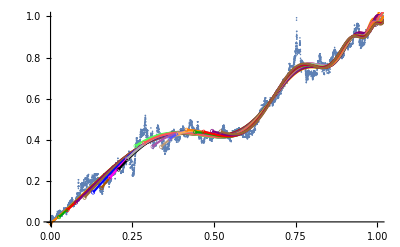

```mathematica
(* Plot of the results: *)
colors={Orange,Darker[Green],Red, Purple, Brown, Blue, Darker[Orange], Magenta,Black, Lighter[Gray], Lighter[Green], Lighter[Red], Lighter[Purple], Lighter[Brown], Lighter[Blue],Lighter[Orange]};
circles=Table[{colors[[Mod[i, Length[colors]]+1]],Thickness[0.0012],Circle[{i stepTi,lpplsModel/.fits[[i+1]]/.ti-> i stepTi},{0.005,0.0085}]}, {i, 0,Length[fits]-1}];
Show[ListPlot[bubbleScaled, ImageSize->Full, Epilog-> circles], Plot[Table[If[ti>i stepTi,Evaluate[lpplsModel/.fits[[i+1]]],""], {i,0,Length[fits]-1}], {ti, 0, maxTc}, PlotStyle->colors, Evaluated->True]]
```

```mathematica
(* 4. Rejection criteria: See if the residuals errors of the fits (ℛerror field) are below the 95% of the simulated (standardized) RSSs: *)
T1s=Subscript[T, 1]/.fits
ℛerrors=ℛerror/.fits
RSSs=RSS/.fits
ℛσs=ℛσ/.fits
```

{0.,0.0260417,0.0520833,0.078125,0.104167,0.130208,0.15625,0.182292,0.208333,0.234375,0.260417,0.286458,0.3125,0.338542,0.364583,0.390625,0.416667,0.442708,0.46875,0.494792,0.520833}

{0.00121174,0.00123648,0.0012655,0.00129162,0.00126083,0.00116198,0.00108623,0.00110844,0.00112713,0.00115286,0.00106721,0.0010598,0.000924559,0.000854442,0.000854044,0.000878072,0.000905668,0.000918804,0.000924276,0.000928424,0.00095679}

{11.1601,11.0912,11.0478,10.9658,10.4019,9.3075,8.4411,8.34769,8.21787,8.12882,7.26879,6.96499,5.85431,5.20526,4.99787,4.92774,4.86525,4.71622,4.52248,4.31996,4.22231}

{0.0347987,0.0351518,0.0355616,0.0359264,0.0354953,0.0340751,0.0329453,0.03328,0.0335589,0.0339394,0.0326538,0.0325397,0.0303922,0.0292165,0.0292091,0.0296164,0.0300775,0.0302941,0.0303833,0.0304504,0.030911}

```mathematica
(* Only last bubble *)
npBestFit=bestFits[[bubble]];
```

```mathematica
nPℓ=Length[npBestFit];
nPℓ
```

9217

```mathematica
(* Plot of the residuals of the non-parametric fit vs the residuals of the parametric fit: *)
(* Non-parametric residuals: *)
npℛs=ℛs[[bubble]];
```

```mathematica
(* Parametric residuals: *)
fullFit[t_]:=lpplsModel/.fits[[1]]/.ti-> t
pℛs=Table[bubbleScaled[[i]][[2]]-fullFit[bubbleScaled[[i]][[1]]],{i,1,Length[bubbleScaled]}];
```

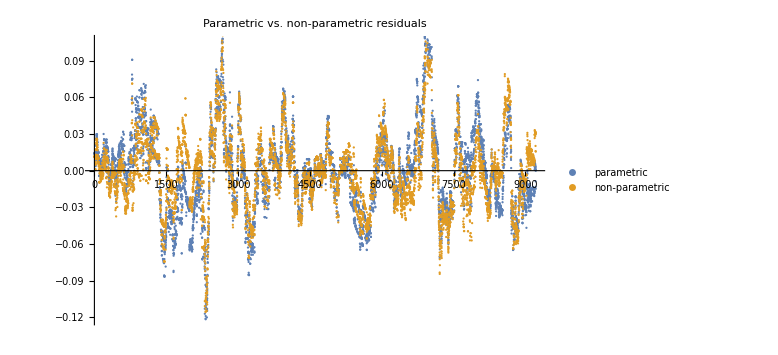

```mathematica
ListPlot[{pℛs,npℛs}, ImageSize->Large, {PlotLabel-> "Parametric vs. non-parametric residuals", PlotLegends->{"parametric","non-parametric"}}]
```

```mathematica
(* RSSs: *)
Total[#^2]&/@{npℛs, pℛs}
```

{8.73805,11.1601}

```mathematica
(* Residual Standard Errors: *)
{√(Total[npℛs^2]/effectiveDfs),√(Total[pℛs^2]/(Length[pℛs]-numParams)) }
```

{0.0308249,0.03481}

```mathematica
(* Mean residual squared error: *)
{Total[npℛs^2]/effectiveDfs,Total[pℛs^2]/(Length[pℛs]-numParams) }
```

{0.000950173,0.00121174}

```mathematica
selN=Length[T1s];
selN
```

21

```mathematica
selNpBestFit=Table[npBestFit[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selNpBestFit
```

{9217,8977,8737,8497,8257,8017,7777,7537,7297,7057,6817,6577,6337,6097,5857,5617,5377,5137,4897,4657,4417}

```mathematica
selBubbleScaled2=Table[bubbleScaled[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selBubbleScaled2
```

{9217,8977,8737,8497,8257,8017,7777,7537,7297,7057,6817,6577,6337,6097,5857,5617,5377,5137,4897,4657,4417}

```mathematica
(* Export selected bubbles: *)
selBubbleScaledCsvs=MapIndexed[Export[base<>"csv/selBubbleScaled-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,selBubbleScaled2];
```

```mathematica
selBubbleScaled=#[[All,2]]&/@selBubbleScaled2;
```

```mathematica
selNpℛs=Table[selBubbleScaled[[i]]-selNpBestFit[[i]], {i, 1,selN}];
```

```mathematica
(* Structural checks: *)
Length/@selNpℛs
```

{9217,8977,8737,8497,8257,8017,7777,7537,7297,7057,6817,6577,6337,6097,5857,5617,5377,5137,4897,4657,4417}

```mathematica
selBubbleScaled[[1]][[1]]==bubbleScaled[[1]][[2]]
selNpBestFit[[1]][[1]]==npBestFit[[1]]
selNpℛs[[1]][[1]]==ℛs[[bubble]][[1]]
```

True

True

True

```mathematica
(* Magnitude of the parametric residual fits: *)
ℛerrors
```

{0.00121174,0.00123648,0.0012655,0.00129162,0.00126083,0.00116198,0.00108623,0.00110844,0.00112713,0.00115286,0.00106721,0.0010598,0.000924559,0.000854442,0.000854044,0.000878072,0.000905668,0.000918804,0.000924276,0.000928424,0.00095679}

```mathematica
RSSs
```

{11.1601,11.0912,11.0478,10.9658,10.4019,9.3075,8.4411,8.34769,8.21787,8.12882,7.26879,6.96499,5.85431,5.20526,4.99787,4.92774,4.86525,4.71622,4.52248,4.31996,4.22231}

```mathematica
(* For each selection, do the simulations, and compute all the statistics: *)
(* Standard deviations: *)
selStdDevℛs=StandardDeviation[#]& /@selNpℛs
```

{0.0307914,0.0311535,0.0315103,0.0318279,0.0320896,0.0322009,0.0322375,0.0322268,0.0324606,0.0328647,0.0318254,0.0313179,0.0305988,0.0306148,0.0302722,0.0307282,0.0312376,0.0312296,0.0314775,0.0320835,0.0328924}

```mathematica
(* 1.c Fit AR(1) error model on the detrended data *)
(* Model the residuals with an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
selEstimatedAR1Models=FindProcessParameters[#,ar1Process]&/@selNpℛs
```

{{ρ→0.954627,σ→-0.00916927,μ→7.67349×10^-6},{ρ→0.954631,σ→-0.00927675,μ→4.14645×10^-7},{ρ→0.954952,σ→-0.00935048,μ→9.09405×10^-6},{ρ→0.955156,σ→-0.00942384,μ→0.0000217391},{ρ→0.95682,σ→-0.0093273,μ→0.000011886},{ρ→0.958043,σ→-0.00922903,μ→-0.0000160107},{ρ→0.958421,σ→-0.00919861,μ→-0.0000210987},{ρ→0.958887,σ→-0.00914495,μ→0.0000114154},{ρ→0.960567,σ→-0.00902504,μ→-4.06379×10^-6},{ρ→0.960385,σ→-0.00915797,μ→3.53617×10^-6},{ρ→0.959769,σ→-0.00893568,μ→0.0000562433},{ρ→0.959616,σ→-0.00880951,μ→1.21009×10^-6},{ρ→0.960611,σ→-0.00850266,μ→-0.0000450196},{ρ→0.96151,σ→-0.00841138,μ→-0.0000497818},{ρ→0.960379,σ→-0.00843606,μ→8.52536×10^-7},{ρ→0.961278,σ→-0.0084673,μ→-7.38841×10^-6},{ρ→0.962813,σ→-0.00843868,μ→-0.0000167284},{ρ→0.961971,σ→-0.00852964,μ→-0.0000563499},{ρ→0.961733,σ→-0.00862356,μ→-0.0000455686},{ρ→0.962134,σ→-0.00874431,μ→-0.0000231797},{ρ→0.962794,σ→-0.00888777,μ→-0.0000249762}}

```mathematica
(* Compute the log-likelihood of the fit *)
selEstimatedProcesses=ar1Process/.#&/@selEstimatedAR1Models
logLikelihoods=Table[LogLikelihood[selEstimatedProcesses[[i]],selNpℛs[[i]]], {i, Length[T1s]}]
```

{ARProcess[7.67349×10^-6,{0.954627},0.0000840755],ARProcess[4.14645×10^-7,{0.954631},0.0000860581],ARProcess[9.09405×10^-6,{0.954952},0.0000874314],ARProcess[0.0000217391,{0.955156},0.0000888088],ARProcess[0.000011886,{0.95682},0.0000869986],ARProcess[-0.0000160107,{0.958043},0.0000851751],ARProcess[-0.0000210987,{0.958421},0.0000846145],ARProcess[0.0000114154,{0.958887},0.0000836301],ARProcess[-4.06379×10^-6,{0.960567},0.0000814514],ARProcess[3.53617×10^-6,{0.960385},0.0000838683],ARProcess[0.0000562433,{0.959769},0.0000798464],ARProcess[1.21009×10^-6,{0.959616},0.0000776074],ARProcess[-0.0000450196,{0.960611},0.0000722953],ARProcess[-0.0000497818,{0.96151},0.0000707513],ARProcess[8.52536×10^-7,{0.960379},0.000071167],ARProcess[-7.38841×10^-6,{0.961278},0.0000716952],ARProcess[-0.0000167284,{0.962813},0.0000712113],ARProcess[-0.0000563499,{0.961971},0.0000727547],ARProcess[-0.0000455686,{0.961733},0.0000743658],ARProcess[-0.0000231797,{0.962134},0.000076463],ARProcess[-0.0000249762,{0.962794},0.0000789925]}

{30167.7,29276.8,28426.6,27578.,26885.1,26194.,25439.7,24693.5,23999.8,23106.4,22488.7,21813.1,21219.6,20484.1,19658.2,18832.,18045.6,17186.4,16338.1,15465.9,14594.7}

```mathematica
(* Step 2: Characterize error variance. *)
(* 2.a Bootstrap the residuals from step 1 and feed them through the fitted AR(1) to simulate errors. *)
selNPointss=Length/@selNpℛs;
nSims=1000;
selSims=ParallelTable[RandomFunction[selEstimatedProcesses[[i]],{0,selNPointss[[i]]-1},nSims], {i,selN}];
selNpℛsPlots=ParallelTable[MapThread[{#1,#2}&,{Range[0,selNPointss[[i]]-1],selNpℛs[[i]][[;;selNPointss[[i]]]]}], {i,selN}];
selPaths=#["Paths"]&/@selSims;
```

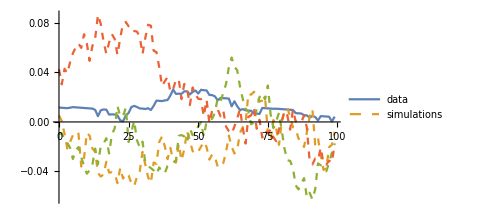
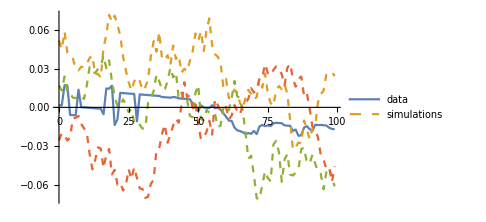
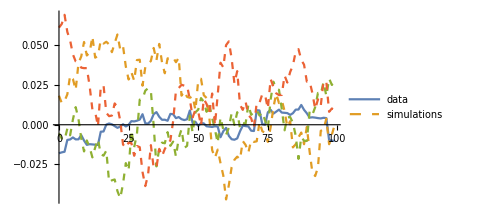
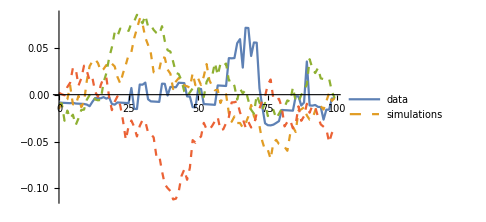
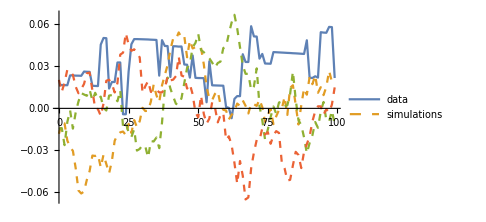
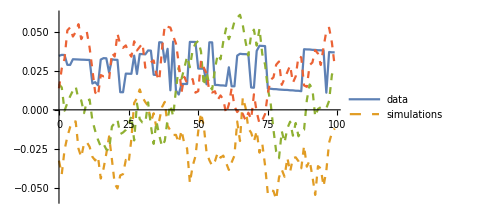
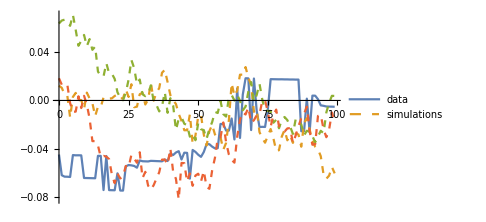
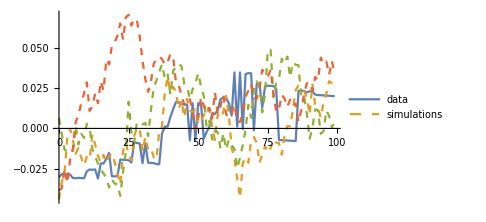

```mathematica
(* Show some simulations and data points *)
showSims=3;
showPoints=100;
Table[ListLinePlot[Join[{selNpℛsPlots[[i]][[;;showPoints]]}, selPaths[[i]][[;;showSims,;;showPoints]]],PlotStyle->{Thick, Dashed, Dashed, Dashed},PlotLegends->{"data","simulations"}, ImageSize->Medium],{i,selN}]
```

```mathematica
(* The estimated number of parameters of the sample selections fits: *)
(* From R's loess, using list of (selections) effective dfs: *)
selRInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@selBubbleScaledCsvs;
```

```mathematica
selRRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@selRInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
selRParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@selRRuns
```

{{15.7242,9196.28},{15.725,8956.27},{15.726,8716.27},{15.7269,8476.27},{15.7279,8236.27},{15.7289,7996.27},{15.7301,7756.27},{15.7312,7516.27},{15.7325,7276.27},{15.7338,7036.26},{15.7353,6796.26},{15.7368,6556.26},{15.7385,6316.26},{15.7403,6076.26},{15.7423,5836.25},{15.7443,5596.25},{15.7467,5356.25},{15.7491,5116.25},{15.7519,4876.24},{15.7548,4636.24},{15.7583,4396.24}}

```mathematica
effectiveDfs
estimatedNParams
(*selEstimatedDfs=Table[Length[selBubbleScaled[[i]]]-estimatedNParams, {i, selN}]*)
selEffectiveDfs=Table[selRParams[[i]][[2]], {i, selN}]
```

9196.28

15.7242

{9196.28,8956.27,8716.27,8476.27,8236.27,7996.27,7756.27,7516.27,7276.27,7036.26,6796.26,6556.26,6316.26,6076.26,5836.25,5596.25,5356.25,5116.25,4876.24,4636.24,4396.24}

```mathematica
(* The "mean" RSSs (RSS/df) of the simulations: *)
selMeanRSSs=Table[Map[Total[(#[[All,2]])^2]/selEffectiveDfs[[i]]&,selPaths[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selMeanRSSs*)
```

```mathematica
memory:=Row[{"Memory Used: ",MemoryInUse[]/1024^3.," GB"}];
Needs["Utilities`CleanSlate`"]
memory
```

Memory Used: 14.9811 GB

```mathematica
Remove[selSims]
Remove[selNpℛsPlots]
memory
```

Memory Used: 14.9812 GB

```mathematica
CleanSlate[];
memory
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 2268945 Kb

Memory Used: 12.8175 GB

```mathematica
(* The standardized "mean" RSSs: *)
selStdMeanRSSs=Table[Map[#/selStdDevℛs[[i]]&,selMeanRSSs[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selStdMeanRSSs*)
```

```mathematica
(* Count *)
selCounts=Table[With[{ℛerror= ℛerrors[[i]]},Select[selMeanRSSs[[i]],#>ℛerror &]//Length],{i,selN}]
```

{0,0,0,1,7,73,285,188,189,201,266,179,569,854,770,754,777,732,726,840,864}

```mathematica
selPValues=Table[selCounts[[i]]/Length[selMeanRSSs[[i]]], {i, selN}]//N
```

{0.,0.,0.,0.001,0.007,0.073,0.285,0.188,0.189,0.201,0.266,0.179,0.569,0.854,0.77,0.754,0.777,0.732,0.726,0.84,0.864}

```mathematica
selRejected=#<(1-0.95)&/@selPValues
```

{True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
(* Take the first / largest interval that is not rejected *)
firstNotRejectedIndex=Select[Table[{i,selRejected[[i]]==False},{i,selN}], #[[2]]&]//First//#[[1]]&
```

6

```mathematica
(* As a fallback (if all rejected), take the one with the min tc *)
minTc=Min[fits[[;;,6,2]]]
```

1.01909

```mathematica
minTcIndex=Select[Table[{i,fits[[i,6,2]]==minTc},{i,selN}],#[[2]]&]//First//#[[1]]&
```

1

```mathematica
index=If[NumericQ[firstNotRejectedIndex], firstNotRejectedIndex,minTcIndex]
```

6

```mathematica
selFit={fits[[index]], "index"-> index}//Flatten
```

{a→1.0282,b→-0.987341,c→-0.0938341,d→-0.127792,T_1→0.130208,tc→1.01909,m→0.8,ω→6.2,RSS→9.3075,ℛerror→0.00116198,ℛσ→0.0340751,LL→26183.3,ρ→0.962288,σ→-0.00926898,μ→2.00079×10^-17,index→6}

```mathematica
bestIndex=index
fit=fits[[bestIndex]]
```

6

{a→1.0282,b→-0.987341,c→-0.0938341,d→-0.127792,T_1→0.130208,tc→1.01909,m→0.8,ω→6.2,RSS→9.3075,ℛerror→0.00116198,ℛσ→0.0340751,LL→26183.3,ρ→0.962288,σ→-0.00926898,μ→2.00079×10^-17}

```mathematica
(* Estimate tc 95% CI by Profile Likelihood *)
m=.
ω=.
tc=.
```

```mathematica
(* Do it over the best params *)
bestm=m/.fit
bestω=ω/.fit
bestTc=tc/.fit
bestLL=LL/.fit
```

0.8

6.2

1.01909

26183.3

```mathematica
t1=Subscript[T, 1]/.fit
```

0.130208

```mathematica
(* Selected best bubble: *)
bubbleBest=Select[bubbleScaled, #[[1]]>= t1&];
```

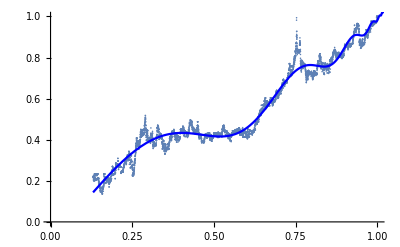

```mathematica
(* Best fit plot *)
Show[ListPlot[bubbleBest, ImageSize->Full], Plot[Evaluate[lpplsModel/.fit], {ti, t1, bestTc}, PlotStyle->{colors[[bestIndex]]}, Evaluated->True]]
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Get nlm function: *)
lpplsModel
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Parametrize it: *)
fit
```

{a→1.0282,b→-0.987341,c→-0.0938341,d→-0.127792,T_1→0.130208,tc→1.01909,m→0.8,ω→6.2,RSS→9.3075,ℛerror→0.00116198,ℛσ→0.0340751,LL→26183.3,ρ→0.962288,σ→-0.00926898,μ→2.00079×10^-17}

```mathematica
bestLppls[x_, testTc_:bestTc]:= lpplsModel/.fit[[1;;4]]/.fit[[7;;8]]/.ti-> x/.tc-> testTc
```

```mathematica
mlℛ = Map[#[[2]]-bestLppls[#[[1]]]&, bubbleBest];
```

```mathematica
(* Fit an AR(1) process (Perhaps re-utilize / recompute the non-parametric residuals model, fitted over the selected interval): *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[mlℛ,ar1Process]
```

{ρ→0.962288,σ→-0.00926898,μ→2.00079×10^-17}

```mathematica
bestLL==LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

True

```mathematica
(* They match. *)
```

```mathematica
(* Now sligthly vary tc, and recompute residuals until the LL is 1.92 times below the max: *)
lowCItc=bestTc;
lowCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/1000;
oldSign=1;
Monitor[While[delta=bestLL-lowCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
lowCItc=lowCItc+ precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], lowCItc]&, bubbleBest];
lowCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],{delta}]
delta
{lowCItc, bestTc}
```

1.92008

{1.01481,1.01909}

```mathematica
(* Let's do the upper leg of the CI: *)
highCItc=bestTc;
highCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/100;
oldSign=-1;
Monitor[While[delta=bestLL-highCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
highCItc=highCItc- precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], highCItc]&, bubbleBest];
highCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],delta]
delta
{lowCItc, bestTc, highCItc}
```

1.92005

{1.01481,1.01909,1.02286}

```mathematica
(* Dates correction: *)
lastScaledTc=bubbleBest[[-1]][[1]]
```

1.00076

```mathematica
(* Now compute the equivalent date of the low CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] lowCItc/lastScaledTc]
```

Sun 25 Jan 2026 09:21:17

```mathematica
(* And the best tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] bestTc/lastScaledTc]
```

Tue 27 Jan 2026 00:47:35

```mathematica
(* And the equivalent date of the high CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] highCItc/lastScaledTc]
```

Wed 28 Jan 2026 11:29:51

```mathematica
(* With the mean tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] meanTc/lastScaledTc]
```

Mon 2 Feb 2026 08:40:40

```mathematica
(* With the max tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] maxTc/lastScaledTc]
```

Tue 10 Feb 2026 00:32:17

```mathematica
(* With the min tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] minTc/lastScaledTc]
```

Tue 27 Jan 2026 00:47:35

```mathematica
(* For reference: *)
{#[[5]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[5]][[2]]/lastScaledTc],#[[6]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[6]][[2]]/lastScaledTc]}&/@fits//TableForm
```

T_1→0. | Wed 1 Jan 2025 00:00:00 | tc→1.01909 | Tue 27 Jan 2026 00:47:35
T_1→0.0260417 | Fri 10 Jan 2025 23:49:03 | tc→1.03732 | Tue 3 Feb 2026 00:39:56
T_1→0.0520833 | Mon 20 Jan 2025 23:38:07 | tc→1.03732 | Tue 3 Feb 2026 00:39:56
T_1→0.078125 | Thu 30 Jan 2025 23:27:11 | tc→1.03732 | Tue 3 Feb 2026 00:39:56
T_1→0.104167 | Sun 9 Feb 2025 23:16:15 | tc→1.01909 | Tue 27 Jan 2026 00:47:35
T_1→0.130208 | Wed 19 Feb 2025 23:05:18 | tc→1.01909 | Tue 27 Jan 2026 00:47:35
T_1→0.15625 | Sat 1 Mar 2025 22:54:22 | tc→1.01909 | Tue 27 Jan 2026 00:47:35
T_1→0.182292 | Tue 11 Mar 2025 22:43:26 | tc→1.01909 | Tue 27 Jan 2026 00:47:35
T_1→0.208333 | Fri 21 Mar 2025 22:32:30 | tc→1.01909 | Tue 27 Jan 2026 00:47:35
T_1→0.234375 | Mon 31 Mar 2025 22:21:33 | tc→1.01909 | Tue 27 Jan 2026 00:47:35
T_1→0.260417 | Thu 10 Apr 2025 22:10:37 | tc→1.01909 | Tue 27 Jan 2026 00:47:35
T_1→0.286458 | Sun 20 Apr 2025 21:59:41 | tc→1.01909 | Tue 27 Jan 2026 00:47:35
T_1→0.3125 | Wed 30 Apr 2025 21:48:45 | tc→1.03732 | Tue 3 Feb 2026 00:39:56
T_1→0.338542 | Sat 10 May 2025 21:37:48 | tc→1.05555 | Tue 10 Feb 2026 00:32:17
T_1→0.364583 | Tue 20 May 2025 21:26:52 | tc→1.05555 | Tue 10 Feb 2026 00:32:17
T_1→0.390625 | Fri 30 May 2025 21:15:56 | tc→1.05555 | Tue 10 Feb 2026 00:32:17
T_1→0.416667 | Mon 9 Jun 2025 21:05:00 | tc→1.03732 | Tue 3 Feb 2026 00:39:56
T_1→0.442708 | Thu 19 Jun 2025 20:54:03 | tc→1.05555 | Tue 10 Feb 2026 00:32:17
T_1→0.46875 | Sun 29 Jun 2025 20:43:07 | tc→1.05555 | Tue 10 Feb 2026 00:32:17
T_1→0.494792 | Wed 9 Jul 2025 20:32:11 | tc→1.05555 | Tue 10 Feb 2026 00:32:17
T_1→0.520833 | Sat 19 Jul 2025 20:21:15 | tc→1.05555 | Tue 10 Feb 2026 00:32:17

```mathematica
(* Compute price at the low leg of the best Tc: *)
bestP=bestLppls[bestTc-epsilon,bestTc]
```

1.02757

```mathematica
lowCIP=bestLppls[lowCItc,bestTc]
```

1.0176

```mathematica
lastScaledP=bubbleBest[[-1]][[2]]
```

0.985239

```mathematica
lastPriceDate
```

2026-01-05

```mathematica
(* Closing price at `lastPriceDate` date: *)
latestPrice=hourlyPrices[[-1]][[2]]
```

4844.64

```mathematica
(* Plot predicted price evolution (USD) :*)
fixDate[brokenDate_]:= StringTake[brokenDate,2]<>"/"<>StringTake[brokenDate,3;;]
ticksH[min_,max_]:=Table[{i,Rotate[fixDate[Block[{$DateStringFormat={"Day","Month","/","YearShort"}},DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]i/lastScaledTc]]], π/3]},{i,{t1,lastScaledTc,lowCItc, bestTc, highCItc}}]
```

```mathematica
ticksVP[min_,max_]:=Table[{i,"$ "<>ToString[IntegerPart[i latestPrice/Exp[lastScaledP]]]},{i,min, max,1/8}]
```

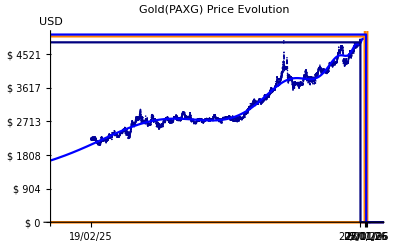

```mathematica
pricePrediction=Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"Silver(KAG) Price Evolution",PlotRange->{{0,maxTc},{0,Exp[bestP]}}, Ticks->{ticksH,ticksVP},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[Exp[lpplsModel/.fit]],UnitStep[ti-lowCItc]Exp[bestP+1],UnitStep[ti-highCItc]Exp[bestP+1]/.fit, UnitStep[lowCItc-ti]Exp[lowCIP],UnitStep[bestTc-ti]Exp[bestP],UnitStep[lastScaledTc-ti]Exp[lastScaledP]}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/Silver(KAG)_PricePrediction-"<>lastPriceDate<>".png",pricePrediction]
```

```mathematica
pToPrice[p_]:= Exp[p] latestPrice/Exp[lastScaledP]
```

```mathematica
(* Check: *)
lastPrice=pToPrice[lastScaledP]
```

4844.64

```mathematica
lowCIPrice=pToPrice[lowCIP]
```

5004.

```mathematica
bestPrice=pToPrice[bestP]
```

5054.14